```mathematica
Remove["Global`*"]
```

```mathematica
(* PacletInstall["https:/rulebasedintegration.org/Rubi-4.16.1.0.paclet"] *)
Get["Rubi`"]
```

```mathematica
ntilde= K/(2(1+ρ (S-1)))(1+Sqrt[1+(4 μ (1 + ρ (S-1)))/((rplus-rminus)K)] );
spec=30.0;
params={δ->0.0,ϕ-> 0.0,K-> 100.0,rplus->2.0,rminus-> 1.0,S->spec,ρ-> 0.1,μ->1.0};
paramsTable={δ->0.0,ϕ-> 0.0,K-> 100.0,rplus->2.0,rminus-> 1.0,S->spec};
assumption = {J-> S * ntilde};
```

#### Now we can expand our master to a FP equation and an equivalent backwards FP: -(∂P(x,t|x_0,t_0))/(∂t)=A(x_0)(∂P)/(∂x_0)+(B(x_0))/2(∂^2 P)/(∂x_0^2)=L_x_0 P For the probability of exiting to the right P_R(x_0) or left P_L(x_0), solve L_x_0 P_R(x_0)=L_x_0 P_R(x_0)=0 with appropriate boundary condition.

#### Our FP

```mathematica
birthFull=(rplus+δ )x+(rplus-rminus) ϕ x(x+ρ J /K)+μ/K;
deathFull=(rminus+δ )x+(rplus-rminus) (1+ϕ) x(x+ρ J /K);
AFull= Simplify[(birthFull-deathFull) ];
BFull= Simplify[(birthFull+deathFull) /K];
```

#### FP used by Mehta & Fisher

```mathematica
birth=(rplus+δ )x+μ/K;
death=(rminus+δ )x+(rplus-rminus) x(x+ρ J /K);
A= Simplify[birth[x,μ,ρ]-death[x,μ,ρ]];
B= (rplus-rminus)x;
```

#### Solving equations

```mathematica
Integrand=FullSimplify[AFull/BFull];
```

```mathematica
potential=FullSimplify[ Integrate[Integrand,x]];
truePotential=potential-(potential/.{x-> 0});
```

```mathematica
optimum=Solve[0==D[truePotential,x],x]/.assumption/.paramsTable ;
```

```mathematica
optimum1[μ_,ρ_]:=Evaluate[x/.optimum[[1,1]]];
optimum2[μ_,ρ_]:=Evaluate[x/.optimum[[2,1]]];
ntildefcn[μ_,ρ_]:=Evaluate[ntilde/.paramsTable];
```

```mathematica
signO1=With[{x:=10^xp/.params,y:=10^yp/. params},Table[optimum1[x,y],{yp,-3,0,0.1},{xp,-3,1,0.1}]];
signO2=With[{x:=10^xp/.params,y:=10^yp/.params},Table[optimum2[x,y],{yp,-3,0,0.1},{xp,-3,1,0.1}]];
ntildeplot=With[{x:=10^xp/.params,y:=10^yp/.params},Table[ntildefcn[x,y],{yp,-3,0,0.1},{xp,-3,1,0.1}]];
```

```mathematica
ListContourPlot[signO1,InterpolationOrder->3,PlotLegends-> Automatic]
ListContourPlot[signO2,InterpolationOrder->3,PlotLegends-> Automatic]
ListContourPlot[ntildeplot,InterpolationOrder->3,PlotLegends-> Automatic]
ListContourPlot[spec ntildeplot,InterpolationOrder->3,PlotLegends-> Automatic]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
truePotAssumed = truePotential/.assumption;
BFullAssumed=BFull/.assumption;
```

```mathematica
IntExpression[μ_?NumericQ,ρ_?NumericQ]:=Evaluate[Exp[2*truePotAssumed]/(BFullAssumed)]
NormFP[μ_,ρ_]:=NIntegrate[(IntExpression[μ,ρ])/.paramsTable,{x,0,4}]
ProbabilityFP[μ_?NumericQ,ρ_?NumericQ]:=((Evaluate[IntExpression[μ,ρ]]/.paramsTable) / NormFP[μ,ρ])
```

```mathematica
NormFP[0.1,0.9];
PFP[y_,μ_,ρ_]:=Re[(ProbabilityFP[μ,ρ]/.x-> y)]
```

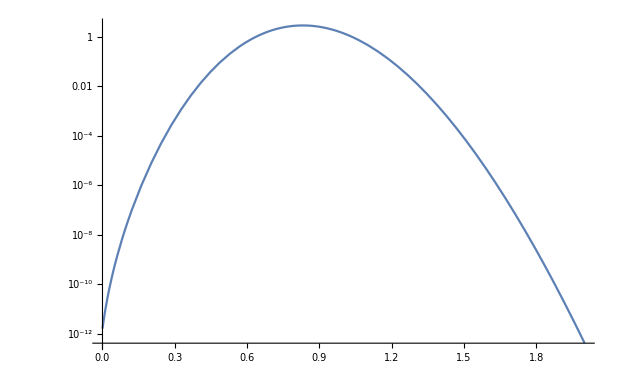

```mathematica
LogPlot[PFP[y,10,0.01],{y,0,2}]
```

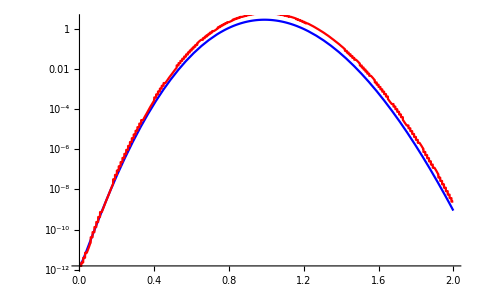

```mathematica
immirate=1.5;
rho=0.0;
MNorm=PFP[0,immirate,rho];
birthrate[n_]:=Simplify[Evaluate[K*birthFull/.x-> n/K]]/. assumption/. paramsTable/. {ρ-> rho,μ-> immirate};
deathrate[n_]:=Simplify[Evaluate[K*deathFull/.x-> n/K]]/. assumption/. paramsTable/.{ρ-> rho,μ-> immirate};
ProbMaster[n_]:=Product[birthrate[i-1]/deathrate[i],{i,1,n}];
Show[{LogPlot[PFP[y,immirate,rho],{y,0,2},PlotStyle-> Blue],LogPlot[MNorm*ProbMaster[x*100],{x,0,2},PlotPoints-> 201,PlotStyle-> Red]}]
```